# Deployment dynamics

```mathematica
(* ==================================================*)(*Plot style for thesis/book figures*)(* ==================================================*)ClearAll[commonPlotOptions,style1,style2,style3,style4,styles2,styles4];

style1=Directive[Black,AbsoluteThickness[2.2]];
style2=Directive[Black,Dashed,AbsoluteThickness[2.2]];
style3=Directive[Black,Dotted,AbsoluteThickness[2.6]];
style4=Directive[Black,DotDashed,AbsoluteThickness[2.2]];

styles2={style1,style2};
styles4={style1,style2,style3,style4};

commonPlotOptions=Sequence[PlotTheme->None,Background->White,Frame->True,Axes->False,FrameStyle->Directive[Black,12],LabelStyle->Directive[Black,12],BaseStyle->{FontFamily->"Times"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],ImageSize->420,PlotRangePadding->Scaled[0.04]];
```

## Unconstrained expanding circle model

### Kinetic energy

The velocity of a point P(r,θ) in the polar plane is:

```mathematica
v=r'[t]×OverHat[r]+r[t]×θ'[t]×OverHat[θ]
```

r̂ r'[t]+θ̂ r[t] θ'[t]

where

```mathematica
r̂=UnitVector[1];
θ̂=UnitVector[2];
```

Thus the kinetic energy of the spring can be expresses as:

```mathematica
T=1/2×ρ×l×(v[[1]]^2+v[[2]]^2)
```

1/2 l ρ (r'[t]^2+r[t]^2 θ'[t]^2)

Where l is the tape length and ρ is the mass density per unit length.
Because l is constant (l’[t]=0), and supposing the point P runs along a circular motion, we have:

```mathematica
len[t_]=r[t]×θ[t]
```

r[t] θ[t]

```mathematica
Solve[len'[t]==0,θ'[t]]
```

{{θ'[t]→-(θ[t] r'[t])/r[t]}}

with θ[t]=l/r[t],

```mathematica
%/.θ[t]->l/r[t]
```

{{θ'[t]→-(l r'[t])/r[t]^2}}

Substituting into T, we have:

```mathematica
T=ReplaceAll[T,%]
```

{1/2 l ρ (r'[t]^2+(l^2 r'[t]^2)/r[t]^2)}

### Potential energy

The elastic potential energy of the coiled spring is:

```mathematica
V=1/2×b×l×(D11/r[t]^2-2×D12/(R×r[t])+D22/R^2)
```

1/2 b l (D22/R^2+D11/r[t]^2-(2 D12)/(R r[t]))

### Lagrangian and solution

Define the Lagrangian of the problem, the initial conditions and the available data. Then solve the equation of motion:

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Lag=FullSimplify[Expand[T[[1]]-V]]
```

(-b l (D11 R^2-2 D12 R r[t]+D22 r[t]^2)+l R^2 ρ (l^2+r[t]^2) r'[t]^2)/(2 R^2 r[t]^2)

```mathematica
eqn=EulerEquations[Lag,r[t],t]
```

l ((b D11+l^2 ρ r'[t]^2)/r[t]^3-ρ r''[t]-(b D12+l^2 R ρ r''[t])/(R r[t]^2))==0

```mathematica
initConds={r[0]==0.055,r'[0]==0};
```

```mathematica
initData={ρ->0.2,l->1,R->0.29,b->0.37,D11->4.53*^-2, D22->4.13*^-2,D12->1.59*^-2};
```

```mathematica
fullEq=Join[{eqn},{initConds}]/. initData;
```

```mathematica
tFinal=1;
```

```mathematica
sol=NDSolve[fullEq,r,{t,0,tFinal}];
```

In the following, tBlossom is the time at which r[t] is exactly equal to l/2π. At t=tBlossom, we have a perfect circle with no overlapping. From this moment on, the tape will deploy as an hinge.

```mathematica
tBlossom=NSolve[r[t]==l/2/Pi/. initData/. sol,t];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
tBlossom=tBlossom[[1]][[1,2]]
```

0.342885

Given the solution and the deployment (blossoming) duration, we show the trajectory of a generic point P(r,θ) in the Cartesian plane for 0<t<tBlossom.

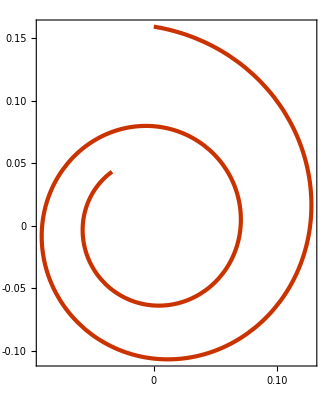

```mathematica
ParametricPlot[r[t] {Sin[l/r[t]],Cos[l/r[t]]}/.initData/.sol,{t,0,tBlossom},PlotTheme->"Web"]
```

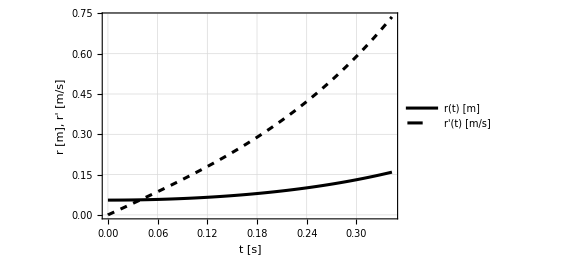

```mathematica
figR=Plot[Evaluate[{r[t]/. initData/. sol,D[r[t]/. initData/. sol,t]}],{t,0,tBlossom},PlotTheme->None,Background->White,Frame->True,Axes->False,FrameLabel->{"t [s]","r [m],  r' [m/s]"},LabelStyle->Directive[Black,12],FrameStyle->Directive[Black,12],BaseStyle->{FontFamily->"Times"},PlotStyle->{Directive[Black,AbsoluteThickness[2.2]],Directive[Black,Dashed,AbsoluteThickness[2.2]]},PlotLegends->Placed[LineLegend[{Directive[Black,AbsoluteThickness[2.2]],Directive[Black,Dashed,AbsoluteThickness[2.2]]},{"r(t) [m]","r'(t) [m/s]"}],{0.25,0.80}],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotRange->All,PlotRangePadding->Scaled[0.04],ImageSize->420]
```

```mathematica
Export["TRES6.pdf",figR]
```

TRES6.pdf

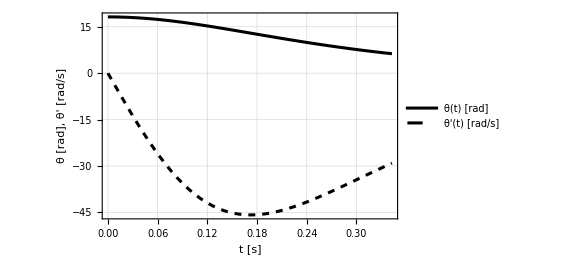

TRES7.pdf

TRES7.png

```mathematica
figTheta=Plot[Evaluate[{l/r[t]/. initData/. sol,D[l/r[t]/. initData/. sol,t]}],{t,0,tBlossom},PlotTheme->None,Background->White,Frame->True,Axes->False,FrameLabel->{"t [s]","θ [rad],  θ' [rad/s]"},LabelStyle->Directive[Black,12],FrameStyle->Directive[Black,12],BaseStyle->{FontFamily->"Times"},PlotStyle->{Directive[Black,AbsoluteThickness[2.2]],Directive[Black,Dashed,AbsoluteThickness[2.2]]},PlotLegends->Placed[LineLegend[{Directive[Black,AbsoluteThickness[2.2]],Directive[Black,Dashed,AbsoluteThickness[2.2]]},{"θ(t) [rad]","θ'(t) [rad/s]"}],{0.70,0.60}],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotRange->All,PlotRangePadding->Scaled[0.04],ImageSize->420]

Export["TRES7.pdf",figTheta]
Export["TRES7.png",figTheta,ImageResolution->600]
```

The total kinetic energy of the system is also given here:

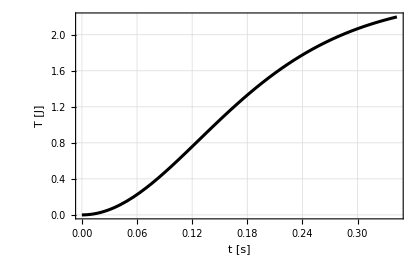

TRES8.pdf

```mathematica
figKineticEnergy=Plot[Evaluate[T/. initData/. sol],{t,0,tBlossom},PlotTheme->None,Background->White,Frame->True,Axes->False,FrameLabel->{"t [s]","T [J]"},LabelStyle->Directive[Black,12],FrameStyle->Directive[Black,12],BaseStyle->{FontFamily->"Times"},PlotStyle->Directive[Black,AbsoluteThickness[2.2]],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotRange->All,PlotRangePadding->Scaled[0.04],ImageSize->420]

Export["TRES8.pdf",figKineticEnergy]
```

The tape tip displacement can be obtained by rotating the original ref frame of θ_0 (assuming the bottom point of the circle is fixed).

```mathematica
Subscript[θ, 0]=-π/2;
```

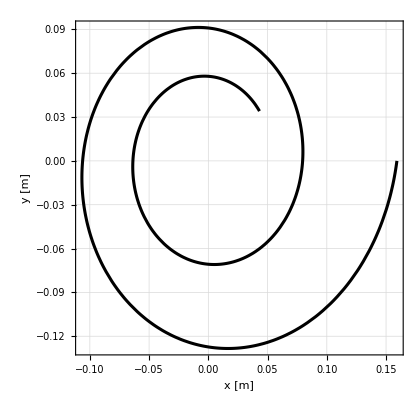

```mathematica
ParametricPlot[Evaluate[r[t] {Sin[l/r[t]-Subscript[θ,0]],Cos[l/r[t]-Subscript[θ,0]]}/. initData/. sol],{t,0,tBlossom},PlotTheme->None,Background->White,Frame->True,Axes->False,FrameLabel->{"x [m]","y [m]"},LabelStyle->Directive[Black,12],FrameStyle->Directive[Black,12],BaseStyle->{FontFamily->"Times"},PlotStyle->Directive[Black,AbsoluteThickness[2.2]],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotRange->All,PlotRangePadding->Scaled[0.04],AspectRatio->1,ImageSize->420]
```

```mathematica
Export["TRES9.pdf",figTrajectory]
Export["TRES9.png",figTrajectory,ImageResolution->600]
```

TRES9.pdf

TRES9.png

## Effect of air drag dissipation

### Air drag dissipation function and drag force

It is assumed here that drag is due to normal flow on the tape surface during the blossoming. Tangential velocity is not affecting drag. Also, the wet area is not constant (A=b×l), but proportional to r; i.e. A=2π×r[t]×b to have:

```mathematica
Dr=1/6×Subscript[ρ, air]×Subscript[C, D]×(2×Pi×r[t]×b)×(v[[1]]^3)
```

1/3 b π r[t] C_D ρ_air r'[t]^3

```mathematica
DrDer=D[Dr,r'[t]]
```

b π r[t] C_D ρ_air r'[t]^2

### New equation and solution

```mathematica
eqn2=Simplify[AddSides[eqn,0==DrDer]]
```

(b D12 l)/R+b π r[t]^3 C_D ρ_air r'[t]^2+l^3 ρ r''[t]+l ρ r[t]^2 r''[t]==(b D11 l+l^3 ρ r'[t]^2)/r[t]

```mathematica
initData2=Join[initData,{Subscript[C, D]->1.1,Subscript[ρ, air]->1.225}];
```

```mathematica
fullEq2=Join[{eqn2},{initConds}]/. initData2;
```

```mathematica
sol2=NDSolve[fullEq2,r,{t,0,tFinal}];
```

New tBlossom to go from fully coiled condition (θ_0=l/r_0) to θ=2π:

```mathematica
tBlossom2=NSolve[r[t]==l/2/Pi/. initData2/. sol2,t];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
tBlossom2=tBlossom2[[1]][[1,2]]
```

0.342939

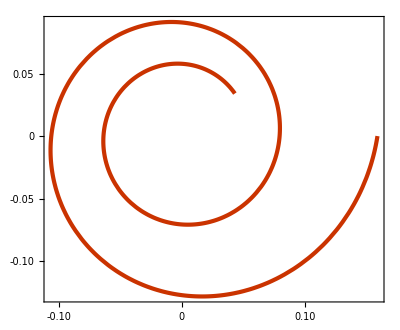

```mathematica
ParametricPlot[r[t] {Sin[l/r[t]-Subscript[θ, 0]],Cos[l/r[t]-Subscript[θ, 0]]}/.initData2/.sol2,{t,0,tBlossom2},PlotTheme->"Web"]
```

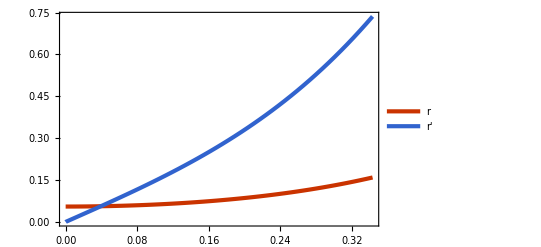

```mathematica
Plot[{Evaluate[r[t]/.initData/.sol2],Evaluate[D[r[t]/.initData2/.sol2,t]]},{t,0,tBlossom2},PlotTheme->"Web",PlotLegends->{r,r'}]
```

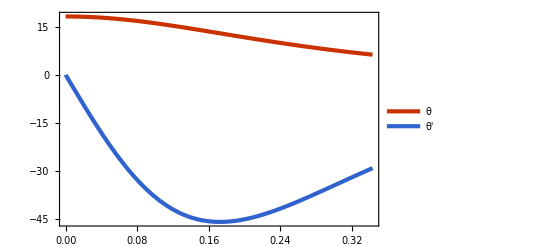

```mathematica
Plot[{Evaluate[l/r[t]/.initData/.sol2],Evaluate[D[l/r[t]/.initData2/.sol2,t]]},{t,0,tBlossom2},PlotTheme->"Web",PlotLegends->{θ,θ'}]
```

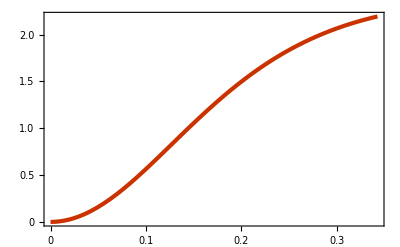

```mathematica
Plot[T/.initData/.sol2,{t,0,tBlossom2},PlotTheme->"Web",PlotRange->All]
```

### Compare the two solutions

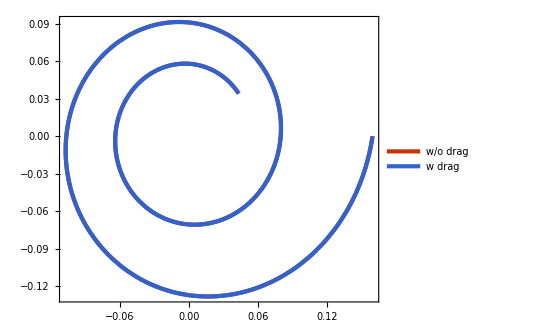

```mathematica
ParametricPlot[{r[t] {Sin[l/r[t]-Subscript[θ, 0]],Cos[l/r[t]-Subscript[θ, 0]]}/.initData/.sol,r[t] {Sin[l/r[t]-Subscript[θ, 0]],Cos[l/r[t]-Subscript[θ, 0]]}/.initData2/.sol2},{t,0,tBlossom},PlotTheme->"Web",PlotLegends->{"w/o drag","w drag"}]
```

## Dragging effect (inertial ref frame)

```mathematica
-Graphics-;
```

We suppose here to write the equations with different constrained point. Previously, the center of the circle was constrained. Now we consider the support to be placed in the bottom-right corner (bottom left in the mirrored figure above), with α=26 deg (0.45 rad), at the initial distance of (-r_0/Tan(α), r_0), so as to have the new ref. frame defined as: x_2=x-Int(r' /Tan(α) dt) - r_0/Tan(α) and y_2=y + Int(r’dt) + r_0. %Data extracted from the experimental results.%

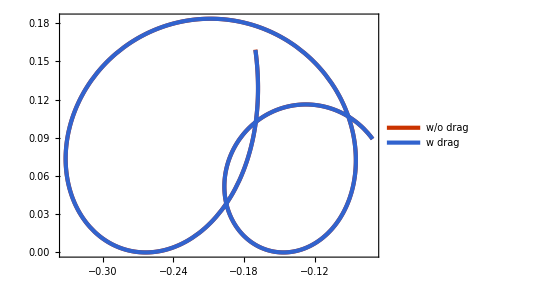

```mathematica
ParametricPlot[{{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData/.sol,{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData2/.sol2},{t,0,tBlossom},PlotTheme->"Web",PlotLegends->{"w/o drag","w drag"}]
```

## Effect of friction

### Friction dissipation energy

The normal force is assumed to be equal to the centrifugal force difference between outer layer and inner layer. In essence, we have F_N=-m (θ')^2 (r_in-r_out)=m (θ')^2 (r_max/r)h, where: r_max=l/2π, r_max/r is the number of overlapping revolutions and h is the tape thickness.

```mathematica
Subscript[F, N]=ρ l θ'[t]^2 Subscript[r, max]/r[t] h/.θ'[t]->-(l r'[t])/r[t]^2 /.Subscript[r, max]->l/2/π
```

(h l^4 ρ r'[t]^2)/(2 π r[t]^5)

Therefore the related Rayleigh dissipation function is:

```mathematica
Fr=1/3 μ Subscript[F, N] r'[t]
```

(h l^4 μ ρ r'[t]^3)/(6 π r[t]^5)

```mathematica
FrDer=D[Fr,r'[t]]
```

(h l^4 μ ρ r'[t]^2)/(2 π r[t]^5)

### New solution with both drag and friction

```mathematica
eqn3=Simplify[AddSides[eqn,0==DrDer+FrDer]]
```

(h l^4 μ ρ r'[t]^2)/r[t]+2 b π^2 r[t]^5 C_D ρ_air r'[t]^2+2 l π ρ r[t]^4 r''[t]+(2 l π r[t]^2 (b D12+l^2 R ρ r''[t]))/R==2 l π r[t] (b D11+l^2 ρ r'[t]^2)

```mathematica
initData3=Join[initData2,{μ->0.65, h->0.33*^-3}];
```

```mathematica
fullEq3=Join[{eqn3},{initConds}]/. initData3;
```

```mathematica
sol3=NDSolve[fullEq3,r,{t,0,tFinal}];
```

New tBlossom to go from fully coiled condition (θ_0=l/r_0) to θ=2π:

```mathematica
tBlossom3=NSolve[r[t]==l/2/Pi/. initData3/. sol3,t];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
tBlossom3=tBlossom3[[1]][[1,2]]
```

0.343384

Here, we show the different solution for time spanning from zero to the tBlossom of the very first case.

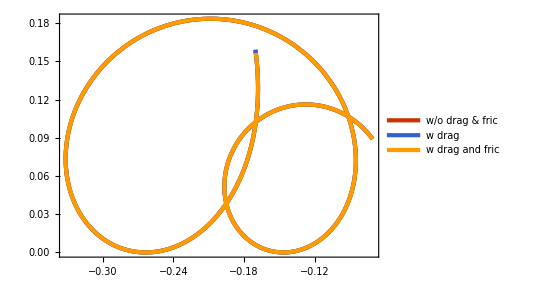

```mathematica
ParametricPlot[{{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData/.sol,{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData2/.sol2,{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData3/.sol3},{t,0,tBlossom},PlotTheme->"Web",PlotLegends->{"w/o drag & fric","w drag","w drag and fric"}]
```

Instead here we show the uncoiling of the latest solution for t = 0 to t = tBlossom3.

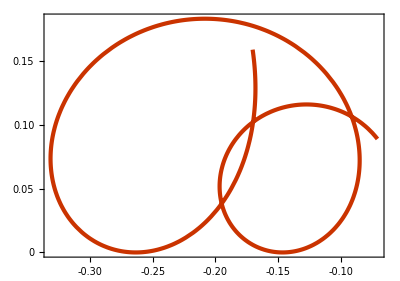

```mathematica
ParametricPlot[{{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData3/.sol3},{t,0,tBlossom3},PlotTheme->"Web"]
```

Comparison with test data:

```mathematica
-Graphics-;
```

## Effect of gravitational potential energy

We suppose here to have V_g=mass x height x g = ρ l g r[t] ∫_(0 -> 2π n_rev) (1+sin θ) dθ

Where n_rev=r_max / r[t] is the number of overlapping revolutions and r_max=l/2π.

```mathematica
Vg=9.81 ρ l r[t] Integrate[(1+Sin[θ]),{θ,0,l/r[t]}]
```

9.81 l ρ (1-Cos[l/r[t]]+l/r[t]) r[t]

```mathematica
V1=V+Vg
```

1/2 b l (D22/R^2+D11/r[t]^2-(2 D12)/(R r[t]))+9.81 l ρ (1-Cos[l/r[t]]+l/r[t]) r[t]

```mathematica
Lag2=T[[1]]-V1
```

-1/2 b l (D22/R^2+D11/r[t]^2-(2 D12)/(R r[t]))-9.81 l ρ (1-Cos[l/r[t]]+l/r[t]) r[t]+1/2 l ρ (r'[t]^2+(l^2 r'[t]^2)/r[t]^2)

```mathematica
eqn4=EulerEquations[Lag2,r[t],t]
```

1/(R r[t]^3)l (1. b D11 R+9.81 l R ρ r[t]^2 Sin[l/r[t]]+1. l^2 R ρ r'[t]^2+R ρ r[t]^3 (-9.81+9.81 Cos[l/r[t]]-1. r''[t])+r[t] (-1. b D12-1. l^2 R ρ r''[t]))==0

```mathematica
eqn5=Simplify[AddSides[eqn4,0==DrDer+FrDer]]
```

(1. h l^4 μ ρ r'[t]^2)/r[t]+19.7392 b r[t]^5 C_D ρ_air r'[t]^2+r[t] (-6.28319 b D11 l-6.28319 l^3 ρ r'[t]^2)+l ρ r[t]^4 (61.638-61.638 Cos[l/r[t]]+6.28319 r''[t])+r[t]^2 ((6.28319 b D12 l)/R+6.28319 l^3 ρ r''[t])==61.638 l^2 ρ r[t]^3 Sin[l/r[t]]

```mathematica
fullEq4=Join[{eqn5},{initConds}]/. initData3;
```

```mathematica
sol4=NDSolve[fullEq4,r,{t,0,tFinal}];
```

```mathematica
tBlossom4=NSolve[r[t]==l/2/Pi/. initData3/. sol4,t];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
tBlossom4=tBlossom4[[1]][[1,2]]
```

0.382759

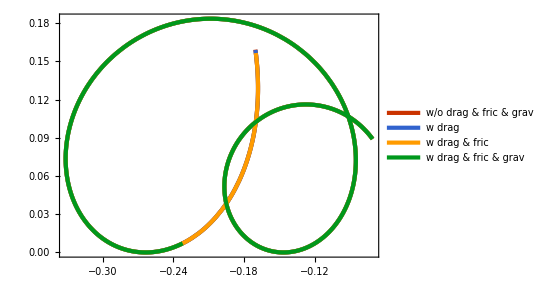

```mathematica
ParametricPlot[{{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData/.sol,{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData2/.sol2,{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData3/.sol3,{r[t] Sin[l/r[t]-Subscript[θ, 0]]-(r[t]-r[0])/Tan[0.45] -r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ, 0]]+(r[t]-r[0])+r[0]}/.initData3/.sol4},{t,0,tBlossom},PlotTheme->"Web",PlotLegends->{"w/o drag & fric & grav","w drag","w drag & fric","w drag & fric & grav"}]
```

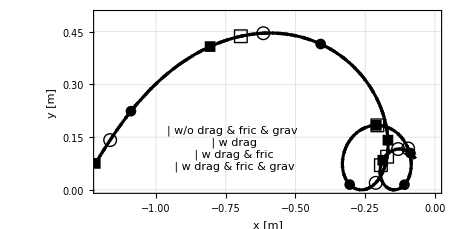

TRES11.pdf

TRES11.png

```mathematica
ClearAll[unwrap,trajSupport,legendEntry];

unwrap[expr_]:=If[ListQ[expr]&&Length[expr]==1&&ListQ[First[expr]],First[expr],expr];

trajSupport[data_,solution_]:=unwrap[{r[t] Sin[l/r[t]-Subscript[θ,0]]-(r[t]-r[0])/Tan[0.45]-r[0]/Tan[0.45],r[t] Cos[l/r[t]-Subscript[θ,0]]+(r[t]-r[0])+r[0]}/. data/. solution];

lineStyles={Directive[Black,AbsoluteThickness[2.2]],Directive[Black,Dashed,AbsoluteThickness[2.2]],Directive[Black,Dotted,AbsoluteThickness[2.8]],Directive[Black,DotDashed,AbsoluteThickness[2.2]]};

labels={"w/o drag & fric & grav","w drag","w drag & fric","w drag & fric & grav"};

markerStyles={Style["●",11,Black],Style["○",13,Black],Style["■",11,Black],Style["□",13,Black]};

trajCurves=ParametricPlot[Evaluate[{trajSupport[initData,sol],trajSupport[initData2,sol2],trajSupport[initData3,sol3],trajSupport[initData3,sol4]}],{t,0,0.6},PlotTheme->None,Background->White,Frame->True,Axes->False,FrameLabel->{"x [m]","y [m]"},LabelStyle->Directive[Black,12],FrameStyle->Directive[Black,12],BaseStyle->{FontFamily->"Times"},PlotStyle->lineStyles,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotRange->{{-1.2,0},{0,0.5}},PlotRangePadding->Scaled[0.04],AspectRatio->0.5,ImageSize->460];

markerTimes={Range[0.04,0.56,0.12],Range[0.07,0.59,0.12],Range[0.10,0.58,0.12],Range[0.13,0.57,0.12]};

markerData={Table[trajSupport[initData,sol]/. t->tt,{tt,markerTimes[[1]]}],Table[trajSupport[initData2,sol2]/. t->tt,{tt,markerTimes[[2]]}],Table[trajSupport[initData3,sol3]/. t->tt,{tt,markerTimes[[3]]}],Table[trajSupport[initData3,sol4]/. t->tt,{tt,markerTimes[[4]]}]};

trajMarkers=ListPlot[markerData,PlotTheme->None,Background->White,Frame->False,Axes->False,PlotStyle->Black,PlotMarkers->markerStyles];

legendEntry[i_]:={Graphics[{lineStyles[[i]],Line[{{0,0},{1,0}}],Inset[markerStyles[[i]],{0.5,0}]},PlotRange->{{0,1},{-0.4,0.4}},ImageSize->{55,16},Background->White],Style[labels[[i]],10,Black]};

customLegend=Framed[Grid[Table[legendEntry[i],{i,1,4}],Alignment->Left,Spacings->{0.6,0.25}],Background->White,FrameStyle->GrayLevel[0.5],RoundingRadius->3,FrameMargins->5];

figTrajectorySupportComparison=Show[trajCurves,trajMarkers,Epilog->Inset[customLegend,Scaled[{0.40,0.25}]]]

Export["TRES11.pdf",figTrajectorySupportComparison]
Export["TRES11.png",figTrajectorySupportComparison,ImageResolution->600]
```

```mathematica
-Graphics-;
```

## Tip velocity

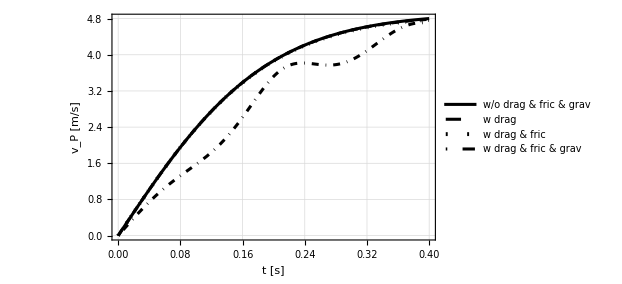

TRES12.pdf

```mathematica
figVelocityComparison=Plot[Evaluate[{Sqrt[Derivative[1][r][t]^2+((l Derivative[1][r][t])/r[t])^2]/. initData/. sol,Sqrt[Derivative[1][r][t]^2+((l Derivative[1][r][t])/r[t])^2]/. initData2/. sol2,Sqrt[Derivative[1][r][t]^2+((l Derivative[1][r][t])/r[t])^2]/. initData3/. sol3,Sqrt[Derivative[1][r][t]^2+((l Derivative[1][r][t])/r[t])^2]/. initData3/. sol4}],{t,0,0.4},PlotTheme->None,Background->White,Frame->True,Axes->False,FrameLabel->{"t [s]","v_P [m/s]"},LabelStyle->Directive[Black,12],FrameStyle->Directive[Black,12],BaseStyle->{FontFamily->"Times"},PlotStyle->{Directive[Black,AbsoluteThickness[2.2]],Directive[Black,Dashed,AbsoluteThickness[2.2]],Directive[Black,Dotted,AbsoluteThickness[2.8]],Directive[Black,DotDashed,AbsoluteThickness[2.2]]},PlotLegends->Placed[LineLegend[{Directive[Black,AbsoluteThickness[2.2]],Directive[Black,Dashed,AbsoluteThickness[2.2]],Directive[Black,Dotted,AbsoluteThickness[2.8]],Directive[Black,DotDashed,AbsoluteThickness[2.2]]},{"w/o drag & fric & grav","w drag","w drag & fric","w drag & fric & grav"}],{0.62,0.28}],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85],Thin],PlotRange->All,PlotRangePadding->Scaled[0.04],ImageSize->460]

Export["TRES12.pdf",figVelocityComparison]
```

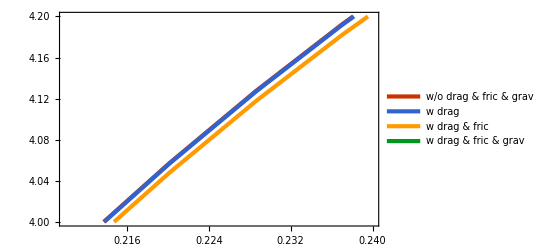

```mathematica
Plot[{{Sqrt[r'[t]^2+((l r'[t])/r[t])^2]}/.initData/.sol,{Sqrt[r'[t]^2+((l r'[t])/r[t])^2]}/.initData2/.sol2,{Sqrt[r'[t]^2+((l r'[t])/r[t])^2]}/.initData3/.sol3,{Sqrt[r'[t]^2+((l r'[t])/r[t])^2]}/.initData3/.sol4},{t,0,0.4},PlotTheme->"Web",PlotLegends->{"w/o drag & fric & grav","w drag","w drag & fric","w drag & fric & grav"},PlotRange->{{0.21,0.24},{4,4.2}}]
```